### Categorization

Tutorial

DoFun

DoFun`

DoFun/tutorial/Known issues

### Keywords

Details

# Known issues

This notebook describes known issues of DoFun.

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

## DSEPlot

### Non-planar diagrams

Non-planar diagrams pose a problem for the used plot program GraphPlot as the following example illustrates:

```mathematica
Needs["DoFun`"]
```

```mathematica
setFields[{phi}];
dse=doDSE[{{phi,4}},{phi,phi,phi,phi}];
dse=Select[dse,Count[#,P[__],∞]==6&];
DSEPlot[dse,{{phi,Black}}]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+^ |  |  |

Clearly, the last diagram is drawn in a disadvantageous way, but the output of doDSE is correct.

Similar problems might occur for other graphs.

## Summing up diagrams

Summing up diagrams may fail for diagrams with more than two loops or fields mixing at the two-point level. The output is correct, though, and the diagrams can be summed up manually.

This affects in particular equations for composite operators.

## Several propagators connecting the same vertex

Mathematica 12 introduced some changes in plotting graphs which either introduced a bug or removed a certain feature on purpose. Thus, at the moment it may cause problems to plot diagrams with more than two propagators connecting the same vertices.

An example where propagators of three different fields connect two vertices, but only two different colors are plotted:

DSEPlotList::multiPropagators: Note: More than two different propagators connecting the same vertices cannot be displayed properly. The plot might contain wrong styles for these propagators.

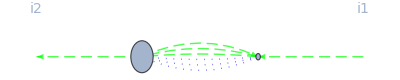
-Graphics-+^

```mathematica
setFields[{A,d},{{c,cb}}];
fieldRules={{A,Red},{c,Green,Dashing[{0.02,0.01}]},{d,Blue,Dotted}};
diag=op[S[{A,r1},{cb,s1},{c,i1},{d,a1},{d,a2},{c,a3},{cb,a4}],P[{c,t1},{cb,s1}],V[{A,u1},{cb,i2},{c,t1},{d,b1},{d,b2},{c,b4},{cb,b3}],P[{A,u1},{A,r1}],P[{d,b1},{d,a1}],P[{d,a2},{d,b2}],P[{c,a3},{cb,b3}],P[{c,b4},{cb,a4}]];
DSEPlot[diag,fieldRules,ImageSize->400]
```

More About

Related Tutorials

Related Wolfram Education Group Courses